1

ρc=1

K=1

ρ0[r]

eqn for m defined

condition for m defined

eqn for p defined

condition for p defined

condition for ρ defined

System defined

Rstar=36.3298km

Rmax=36.3298km

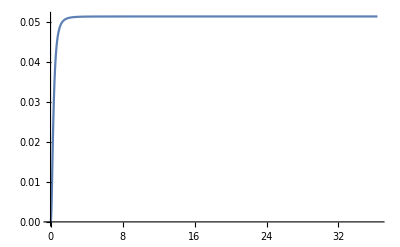

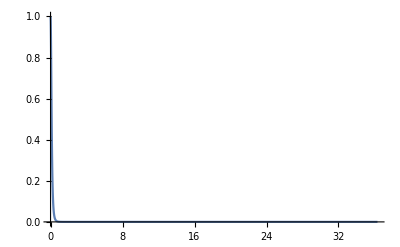

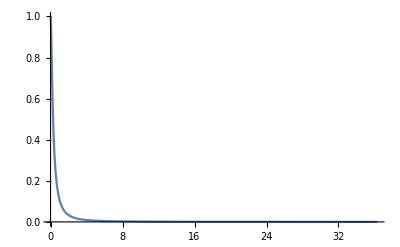

Radius=36.3298

Mass=0.0512661

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
my0=10^(-4);
pc:=1;
κ:=0.3;
ρc:=1;
K=1
Print["ρc=",ρc];
Print["K=",K];
(*eqnState:={p[r]==K*ρ[r]^(κ)}*)
(*ρ[r_]:=(p[r]/K)^(1/κ);
Print["ρ defined"];*)
(*p[r_]:=K*(ρ[r])^(κ);
Print["p defined"];*)
ρ[r_]=ρ0[r]
p[r_]=K*(ρ0[r])^(κ);
eqnM:={m'[r]==4 π r^2 ρ[r]}
Print["eqn for m defined"];
condM:={m[my0]==0}
(*condM:={m[my0]==4 π ρc+(K*ρc^κ)/(κ-1) my0^3 / 3}*)
Print["condition for m defined"];
eqnP:={-p'[r]==(ρ[r]+p[r])*(m[r]+4*π*r^3*p[r])/(r^2*(1-2*m[r]/r))}
Print["eqn for p defined"];
condP:={p[my0]==pc}
Print["condition for p defined"];
condρ:={ρ[my0]==ρc}
Print["condition for ρ defined"];
stopCond:={WhenEvent[Evaluate[Re[ρ0[r]]<=0],rMax=r;"StopIntegration"]}
system:=Join[eqnM,eqnP,condM,condρ, stopCond];
Print["System defined"];
state=First[NDSolve`ProcessEquations[system, {m,ρ0}, {r, my0, ∞}]];
NDSolve`Iterate[state,∞]
sol=NDSolve`ProcessSolutions[state];

rStar=Last[state@"CurrentTime"[]];
Print["Rstar=",rStar,"km"];
Print["Rmax=",rMax,"km"];
rMax:=rStar
(*sol=NDSolve[system, {p}, {r, my0, ∞}];*)
Off[Solve::ifun];
Plot[Evaluate[m[r]/.sol],{r,my0,rMax},PlotRange->All]
Plot[Evaluate[ρ0[r]/.sol],{r,my0,rMax},PlotRange->All]
Plot[Evaluate[p[r]/.sol],{r,my0,rMax},PlotRange->All]
(*sol2 = NDReduce[system, {m,ρ}, {r, my0, 20}]
Plot[Evaluate[m[r]/.sol2],{r,my0,rMax}]
Plot[Evaluate[ρ[r]/.sol2],{r,my0,rMax}]
Plot[Evaluate[p[r]/.sol2],{r,my0,rMax}]*)
Print["Radius=",rMax,""];
Print["Mass=",Evaluate[m[rMax]/.sol],""];
```